## Functions for modeling

UNITS:
	cij: GPa;
	x: km;
	t: s;
	k: 1/m

### Linear-solid stiffness matrix

cij0[i], Q0[i] are assumed defined for each layer i

```mathematica
cijCarcione[pars_,ω0_,ω_]:=Module[{c11i,c13i,c33i,c44i,ρi,Q01i,Q02i},

{c11i,c13i,c33i,c44i,ρi,Q01i,Q02i}=pars;

{(2 c44i ω ((√(1+Q01i^2)-√(1+Q02i^2)) ω+ⅈ (Q01i-Q02i) ω0)+c33i ω ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0)+c11i (√(1+Q01i^2) ω+ⅈ Q01i ω0) ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0))/(((-1+√(1+Q01i^2)) ω+ⅈ Q01i ω0) ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0)),c13i-(2 c44i ω ((-2+√(1+Q01i^2)+√(1+Q02i^2)) ω+ⅈ (Q01i+Q02i) ω0))/(((-1+√(1+Q01i^2)) ω+ⅈ Q01i ω0) ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0))+c11i/(-1+√(1+Q01i^2)+(ⅈ Q01i ω0)/ω)+c33i/(-1+√(1+Q01i^2)+(ⅈ Q01i ω0)/ω),(2 c44i ω ((√(1+Q01i^2)-√(1+Q02i^2)) ω+ⅈ (Q01i-Q02i) ω0)+c11i ω ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0)+c33i (√(1+Q01i^2) ω+ⅈ Q01i ω0) ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0))/(((-1+√(1+Q01i^2)) ω+ⅈ Q01i ω0) ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0)),(c44i (ω+√(1+Q02i^2) ω+ⅈ Q02i ω0))/((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0),ρi}//N

]
```

```mathematica
cijCarcioneCompiled=
Compile[{{cijQρ,_Real, 1},{ω0,_Real},{ω,_Complex}},
Module[{c11i,c13i,c33i,c44i,ρi,Q01i,Q02i},

c11i=cijQρ[[1]];
c13i=cijQρ[[2]];
c33i=cijQρ[[3]];
c44i=cijQρ[[4]];
ρi=cijQρ[[5]];
Q01i=cijQρ[[6]];
Q02i=cijQρ[[7]];

{(2 c44i ω ((√(1+Q01i^2)-√(1+Q02i^2)) ω+ⅈ (Q01i-Q02i) ω0)+c33i ω ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0)+c11i (√(1+Q01i^2) ω+ⅈ Q01i ω0) ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0))/(((-1+√(1+Q01i^2)) ω+ⅈ Q01i ω0) ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0)),c13i-(2 c44i ω ((-2+√(1+Q01i^2)+√(1+Q02i^2)) ω+ⅈ (Q01i+Q02i) ω0))/(((-1+√(1+Q01i^2)) ω+ⅈ Q01i ω0) ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0))+c11i/(-1+√(1+Q01i^2)+(ⅈ Q01i ω0)/ω)+c33i/(-1+√(1+Q01i^2)+(ⅈ Q01i ω0)/ω),(2 c44i ω ((√(1+Q01i^2)-√(1+Q02i^2)) ω+ⅈ (Q01i-Q02i) ω0)+c11i ω ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0)+c33i (√(1+Q01i^2) ω+ⅈ Q01i ω0) ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0))/(((-1+√(1+Q01i^2)) ω+ⅈ Q01i ω0) ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0)),(c44i (ω+√(1+Q02i^2) ω+ⅈ Q02i ω0))/((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0),Re@ρi}

],CompilationTarget->"C", RuntimeOptions->"Speed"
];
```

```mathematica
cijLS[{c11i_,c13i_,c33i_,c44i_,ρi_,Q01i_,Q02i_},ω0_,ω_]:=cijCarcioneCompiled[{c11i,c13i,c33i,c44i,ρi,Q01i,Q02i},ω0,ω];
```

### Slowness, L1/L2 matrices

Requires run of the cijCarcione function to get frequency-dependent cij[i]

```mathematica
GetLStovasUrsin[{c11i_, c13i_, c33i_, c44i_, ρi_},p_]:=Module[
{L1,L2,d1,d2,d3,d4,d5,qα,qβ,α0,β0,η,δ,σ0,Sα,Sβ,R,R1,R2,req1,req2,imq1,imq2},
α0=√(c33i/ρi);
β0=√(c44i/ρi);
σ0=1-c44i/c33i;
δ=(c13i-c33i+2c44i)/c33i;
η=(c11i c33i-(c13i+2c44i)^2)/(2 c33i^2);
R1=2(1-p^2 β0^2)(δ+2 p^2 α0^2 η)^2;
R2=σ0+2 p^2 β0^2 δ-2 p^2 α0^2(1-2 p^2 β0^2)η;
R=R1/(R2+√(R2^2+2 p^2 β0^2 R1));
Sα=2δ+2 p^2 α0^2 η+R;
Sβ=2(1-p^2 β0^2)α0^2/β0^2 η-R;

d2=√((σ0+δ)/(σ0+Sα));
d3=2 β0^2(σ0+1/2(Sα+δ))/(σ0+δ);
d4=√((σ0-p^2 β0^2(σ0+Sβ))/((1-p^2 β0^2(1+Sβ))(σ0+δ)));
d5=(σ0-2 p^2 β0^2(σ0+1/2(Sβ+δ)))/(σ0+δ);
d1=1/(√(p^2 d3+d5));


req1=Re[1/α0^2-p^2-p^2 Sα];
req2=Re[1/β0^2-p^2-p^2 Sβ];
imq1=Im[1/α0^2-p^2-p^2 Sα];
imq2=Im[1/β0^2-p^2-p^2 Sβ];
imq1=Sign[imq1]imq1;
imq2=Sign[imq2]imq2;
req1=req1;
req2=req2;

qα=√(req1+ⅈ imq1);
qβ=√(req2+ⅈ imq2);

(*qα=1/α0^2-p^2-p^2 Sα;
qβ=1/β0^2-p^2-p^2 Sβ;*)
(*
qα=Sign[Im[qα]]qα;
qβ=Sign[Im[qβ]]qβ;*)



L1=d1{
{d2 √(qα/ρi),1/d4 p/(√(ρi qβ))},
{d3 d2 p √(ρi qα),-d5/d4 √(ρi/qβ)}
};

L2=d1{
{d5/d2 √(ρi/qα),d3 d4 p √(ρi qβ)},
{1/d2 p/(√(ρi qα)),-d4 √(qβ/ρi)}
};

(*{{qα,qβ},{L1,L2}}*)
{{{qα,0},{0,qβ}},L1,L2}
(*l1[j]=L1//N;
l2[j]=L2//N;
q1[j]=qα//N;
q2[j]=qβ//N;*)

]
```

```mathematica
qLCompiled=
Compile[{{cij,_Complex, 1},{ρi,_Real},{p,_Complex}},
Module[
{L1,L2,d1,d2,d3,d4,d5,qα,qβ,α0,β0,η,δ,σ0,Sα,Sβ,R,R1,R2},
α0=√(cij[[3]]/ρi);
β0=√(cij[[4]]/ρi);
σ0=1-cij[[4]]/cij[[3]];
δ=(cij[[2]]-cij[[3]]+2cij[[4]])/cij[[3]];
η=(cij[[1]] cij[[3]]-(cij[[2]]+2cij[[4]])^2)/(2 cij[[3]]^2);
R1=2(1-p^2 β0^2)(δ+2 p^2 α0^2 η)^2;
R2=σ0+2 p^2 β0^2 δ-2 p^2 α0^2(1-2 p^2 β0^2)η;
R=R1/(R2+√(R2^2+2 p^2 β0^2 R1));
Sα=2δ+2 p^2 α0^2 η+R;
Sβ=2(1-p^2 β0^2)α0^2/β0^2 η-R;

qα=(Re@#+ⅈ Abs@Im@#)&@√(1/α0^2-p^2-p^2 Sα);
qβ=(Re@#+ⅈ Abs@Im@#)&@√(1/β0^2-p^2-p^2 Sβ);
d2=√((σ0+δ)/(σ0+Sα));
d3=2 β0^2(σ0+1/2(Sα+δ))/(σ0+δ);
d4=√((σ0-p^2 β0^2(σ0+Sβ))/((1-p^2 β0^2(1+Sβ))(σ0+δ)));
d5=(σ0-2 p^2 β0^2(σ0+1/2(Sβ+δ)))/(σ0+δ);
d1=1/(√(p^2 d3+d5));
L1=d1{
{d2 √(qα/ρi),1/d4 p/(√(ρi qβ))},
{d3 d2 p √(ρi qα),-d5/d4 √(ρi/qβ)}
};

L2=d1{
{d5/d2 √(ρi/qα),d3 d4 p √(ρi qβ)},
{1/d2 p/(√(ρi qα)),-d4 √(qβ/ρi)}
};

{{{qα,0},{0,qβ}},L1,L2}
],CompilationTarget->"C", RuntimeOptions->"Speed"
];
```

```mathematica
qL[{c11i_, c13i_, c33i_, c44i_, ρi_},p_]:=qLCompiled[{c11i, c13i, c33i, c44i}, ρi,p];
```

### Reflectivity and transmissivity

```mathematica
(*
REFLECTIVITY ONLY
*)
stackRefExperiment2[ω_,p_,CijsAndρ:{{_,_,_,_,_}..}, d_List]/;(ArrayQ[d]&&(Length@d==Length@CijsAndρ)):=Module[{qABArray, L1ar,L2ar, L12Array,CArray,DArray,refArray, transArray, phaseArray, foldArray,f},
{qABArray, L1ar, L2ar}=Transpose[qL[#,p]&/@CijsAndρ];
L12Array=Transpose@{L1ar, L2ar};
{CArray,DArray}=Transpose@MapThread[
{Transpose[#1[[2]]].#2[[1]],Transpose[#1[[1]]].#2[[2]]}&,
{RotateLeft@L12Array,L12Array}];
{transArray , refArray}=Transpose@MapThread[{2Transpose@Inverse[#1+#2],Transpose[(#1-#2)].Transpose@Inverse[#1+#2]}&,{CArray, DArray}];
phaseArray=Exp[ⅈ ω(qABArray d)]-ConstantArray[{{0.,1.},{1.,0.}},Length[d]]//Chop;
foldArray=Reverse@Most@Transpose[{transArray,refArray, phaseArray}];
f=(#4.(#3+Transpose[#2].#1.Inverse[IdentityMatrix[2]+#3.#1].#2).#4)&;
Fold[f[#1,#2[[1]],#2[[2]],#2[[3]]]&,{{0,0},{0,0}},foldArray](*;
{transArray,refArray, phaseArray}*)
(*foldArray=Reverse@Most@Transpose[{transArray,refArray, phaseArray}]*)
(*;
phaseArray=Exp[ⅈ ω(qABArray d)];
foldArray=Reverse@Most@Transpose[{transArray,refArray, phaseArray}]*)
]
```

```mathematica
(*
BOTH REFLECTIVITY AND TRANSMISSIVITY
OUPUT[[1]] IS TRANSMISSIVITY MATRIX
OUPUT[[2]] IS REFLECTIVITY MATRIX
*)
stackRefExperiment2RT[ω_,p_,CijsAndρ:{{_,_,_,_,_}..}, d_List]/;(ArrayQ[d]&&(Length@d==Length@CijsAndρ)):=Module[{qABArray, L1ar,L2ar, L12Array,CArray,DArray,refArray, transArray, phaseArray, foldArray,fR,fT},
{qABArray, L1ar, L2ar}=Transpose[qL[#,p]&/@CijsAndρ];
L12Array=Transpose@{L1ar, L2ar};
{CArray,DArray}=Transpose@MapThread[
{Transpose[#1[[2]]].#2[[1]],Transpose[#1[[1]]].#2[[2]]}&,
{RotateLeft@L12Array,L12Array}];
{transArray , refArray}=Transpose@MapThread[{2Transpose@Inverse[#1+#2],Transpose[(#1-#2)].Transpose@Inverse[#1+#2]}&,{CArray, DArray}];
phaseArray=Exp[ⅈ ω(qABArray d)]-ConstantArray[{{0.,1.},{1.,0.}},Length[d]]//Chop;
foldArray=Reverse@Most@Transpose[{transArray,refArray, phaseArray}];
fR=(#4.(#3+Transpose[#2].#1.Inverse[IdentityMatrix[2]+#3.#1].#2).#4)&;
fT=(#1.Inverse[IdentityMatrix[2]+#3.fR[#5,#2,#3,#4]].#2.#4)&;
Fold[
{fT[#1[[1]],#2[[1]],#2[[2]],#2[[3]],#1[[2]]],
fR[#1[[2]],#2[[1]],#2[[2]],#2[[3]]]}&,{{{1,0},{0,1}},{{0,0},{0,0}}},foldArray]
]
```

```mathematica
<<CompiledFunctionTools`
```

```mathematica
stackRefExperiment[ω_,p_,CijsAndρ:{{_,_,_,_,_}..}, d_List]/;(ArrayQ[d]&&(Length@d==Length@CijsAndρ)):=Module[{qABArray,L1ar,L2ar, L12Array,CArray,DArray,refArray, transArray, phaseArray, foldArray,f},
{qABArray, L1ar, L2ar}=Transpose[GetLStovasUrsin[#,p]&/@CijsAndρ];
L12Array=Transpose@{L1ar, L2ar};
{CArray,DArray}=Transpose@MapThread[
{Transpose[#1[[2]]].#2[[1]],Transpose[#1[[1]]].#2[[2]]}&,
{RotateLeft@L12Array,L12Array}];
{transArray , refArray}=Transpose@MapThread[{2Transpose@Inverse[#1+#2],Transpose[(#1-#2)].Transpose@Inverse[#1+#2]}&,{CArray, DArray}];
phaseArray=Exp[ⅈ ω(qABArray d)]-ConstantArray[{{0.,1.},{1.,0.}},Length[d]]//Chop;
foldArray=Reverse@Most@Transpose[{transArray,refArray, phaseArray}];
f=(#4.(#3+Transpose[#2].#1.Inverse[IdentityMatrix[2]+#3.#1].#2).#4)&;
Fold[f[#1,#2[[1]],#2[[2]],#2[[3]]]&,{{0,0},{0,0}},foldArray]
]
```

```mathematica
stackRefTransCoefs[ω_,p_,CijsAndρ:{{_,_,_,_,_}..}, d_List]/;(ArrayQ[d]&&(Length@d==Length@CijsAndρ)):=Module[{qABArray,L1ar,L2ar, L12Array,CArray,DArray,refArray, transArray, phaseArray, foldArray,f},
{qABArray, L1ar, L2ar}=Transpose[GetLStovasUrsin[#,p]&/@CijsAndρ];
L12Array=Transpose@{L1ar, L2ar};
CArray=MapThread[Transpose[#1].#2&,{RotateLeft@L12Array[[;;,2]],L12Array[[;;,1]]}];
DArray=MapThread[Transpose[#1].#2&,{RotateLeft@L12Array[[;;,1]],L12Array[[;;,2]]}];
transArray=2Transpose/@ Inverse/@(CArray+DArray);
refArray=1/2 MapThread[#1.#2&,{Transpose/@(CArray-DArray),transArray}];
phaseArray=Exp[ⅈ ω(qABArray d)]-ConstantArray[{{0.,1.},{1.,0.}},Length[d]]//Chop;
foldArray=Reverse@Most@Transpose[{transArray,refArray, phaseArray}];
f=(#4.(#3+Transpose[#2].#1.Inverse[IdentityMatrix[2]+#3.#1].#2).#4)&;
Fold[f[#1,#2[[1]],#2[[2]],#2[[3]]]&,{{0,0},{0,0}},foldArray]
]
```

### Time-domain description

```mathematica
addSrcRec[RT_,ω_,zs_,zr_,qAB1_]:=Module[
{exp},

exp[z_]:=Exp[ⅈ ω z qAB1]-{{0,1},{1,0}};

exp[zr].RT.exp[zs]//N//Chop

]

(*
NOTE THAT RPP IS TAKEN FOR INTEGRATION ([[1,1]] after the StackRefExperiment function)
*)

integrandp[x_,p_?NumericQ,ω_?NumericQ,CijsAndρ:{{_,_,_,_,_}..},dList_,zs_,zr_]:=With[{p0=p},
addSrcRec[
stackRefExperiment2[ω,p0,CijsAndρ, dList],ω,zs,zr,qL[CijsAndρ[[1]],p0][[1]]][[1,1]] BesselJ[0,x p0 ω]p0 ω^2]

integrandk[x_,k_?NumericQ,ω_?NumericQ,CijsAndρ:{{_,_,_,_,_}..},dList_,zs_,zr_]:=With[{k0=1000k},
addSrcRec[
stackRefExperiment2[ω,k0/ω,CijsAndρ, dList],ω,zs,zr,qL[CijsAndρ[[1]],k0/ω][[1]]][[1,1]] BesselJ[0,x k0]k0]

(*VARIABLE UPPER BOUNDARY FOR INTEGRATION*)
upperB[f_,fm_,p0_,pm_]:=p0+f/fm pm
rickerF[f_,fp_]:=Module[{ω=2Pi f,ωp=2Pi fp},(2 ω^2)/(√Pi ωp^3)Exp[-(ω/ωp)^2]//N]
integrateNow[f_,offset_,{zs_,zr_},maxfreq_,model_,dList_,ω0_,{slope0_,slopeEnd_}]:=Module[{ωc=2Pi f},
NIntegrate[
integrandk[offset,k,ωc,cijLS[#,ω0,ωc]&/@model,dList,zs,zr],{k,0,upperB[f,maxfreq,slope0,slopeEnd]},
Method->{"GlobalAdaptive","MaxErrorIncreases"->2000},MaxRecursion->Infinity,WorkingPrecision->MachinePrecision,PrecisionGoal->8,AccuracyGoal->Infinity]
];
```

### Numerical testing

```mathematica
overburden={vp^2 den,vp^2 den-2 vs^2 den,vp^2 den,vs^2 den,den,500,500}/.vp->2.5/.vs->1.2/.den->1.8;
binarymodel={
(*shale*)
{22.56,12.38,17.35,3.15,2.38,100,50},
(*sandstone*)
{26.73,12.51,26.73,7.11,2.22,150,100}(*,
(*siltstone*)
{60.13,38.26,50.87,17.17,2.18,100,50}*)
};
```

```mathematica
nrep=2;
model=Join[{overburden},Flatten[ConstantArray[binarymodel,{nrep}],1]];
```

```mathematica
SeedRandom[2018];
dList=ArrayPad[RandomReal[{0,1},Length[model]-2],1];
```

```mathematica
ωcomp=2 Pi 40;
ω0=2Pi 150;
```

```mathematica
cijsNum=cijLS[#,ω0,ωcomp ]&/@model;
```

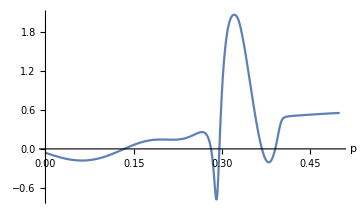
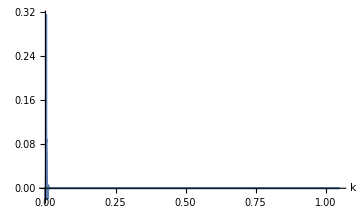

```mathematica
With[{x=1,zs=0.4,zr=0.3,ω=2Pi 1},
{
Plot[
Re@integrandp[x,p+.005I,ω,cijLS[#,ω0,ω]&/@model,dList,zs,zr],{p,0,.5},PlotRange->{Automatic,Full},AxesLabel->Automatic,ImageSize->Medium],
Plot[
Re@integrandk[x,k ,ω,cijLS[#,ω0,ω]&/@model,dList,zs,zr],{k,0,1.05},PlotRange->{Automatic,Full},AxesLabel->Automatic,ImageSize->Medium]
}
]
```

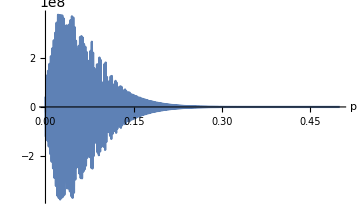
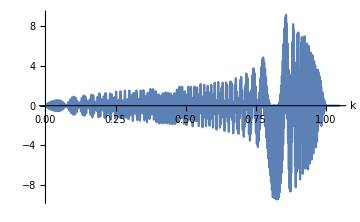

```mathematica
With[{x=1,zs=0.4,zr=0.3,ω=2Pi 400},
{
Plot[
Im@integrandp[x,p+.005I,ω,cijLS[#,ω0,ω]&/@model,dList,zs,zr],{p,0,.5},PlotRange->{Automatic,Full},AxesLabel->Automatic,ImageSize->Medium],
Plot[
Im@integrandk[x,k ,ω,cijLS[#,ω0,ω]&/@model,dList,zs,zr],{k,0,1.05},PlotRange->{Automatic,Full},AxesLabel->Automatic,ImageSize->Medium]
}
]
```

```mathematica
With[{x=1,zs=.1,zr=.2},
integrateNow[10,x,{zs,zr},200,model,dList,ω0,{.1,.6}]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-0.00245055-0.00931965 ⅈ

### Numerical testing: compute single trace

```mathematica
deltafreq=1;
maxfreq=400;
freqvec=Table[f,{f,1,maxfreq,deltafreq}];
fricker=30;
```

```mathematica
With[{x=1,zs=.4,zr=.3,fmax=maxfreq},
{singleTrace,srcF}=Transpose[
ParallelTable[{Quiet@integrateNow[freqvec[[i]],x,{zs,zr},fmax,model,dList,ω0,{.05,1.1}],rickerF[freqvec[[i]],fricker]},{i,1,Length@freqvec}]]
];
```

{{0.000244958+0.000263635 ⅈ,-0.000511003-0.000501295 ⅈ,0.000659238+0.000614564 ⅈ,-0.00102476-0.000903245 ⅈ,0.00149996+0.00149187 ⅈ,-0.00205737-0.00177858 ⅈ,0.00281281+0.00174431 ⅈ,-0.00317465-0.0016818 ⅈ,0.00326829+0.00157101 ⅈ,-0.0041249-0.00170613 ⅈ,0.00531721+0.0023224 ⅈ,-0.0059095-0.00189154 ⅈ,0.00677364+0.000820193 ⅈ,-0.00731055-0.000714732 ⅈ,0.00698578+0.000892268 ⅈ,-0.00767455+0.0000294439 ⅈ,0.00986569-0.000807989 ⅈ,-0.0108804+0.00110012 ⅈ,0.010061-0.0022031 ⅈ,-0.00966308+0.00363236 ⅈ,0.0106357-0.00398078 ⅈ,-0.0112225+0.00423219 ⅈ,0.0116539-0.00631706 ⅈ,-0.0123529+0.00820419 ⅈ,0.0117457-0.00870895 ⅈ,-0.0103562+0.00949968 ⅈ,0.0106959-0.0106905 ⅈ,-0.0111407+0.0116445 ⅈ,0.010316-0.0141398 ⅈ,-0.00992509+0.0166081 ⅈ,0.00934903-0.0162315 ⅈ,-0.00695007+0.0157542 ⅈ,0.00592258-0.0182223 ⅈ,-0.00655785+0.0201282 ⅈ,0.00489273-0.020733 ⅈ,-0.00180889+0.0221268 ⅈ,0.000886649-0.0231741 ⅈ,-0.000558097+0.0220947 ⅈ,-0.00193993-0.0220624 ⅈ,0.00447607+0.0244829 ⅈ,-0.00600791-0.0258007 ⅈ,0.00804876+0.0247212 ⅈ,-0.010464-0.0240445 ⅈ,0.0112358+0.0239116 ⅈ,-0.0131402-0.0228928 ⅈ,0.0168997+0.0232496 ⅈ,-0.0191364-0.023636 ⅈ,0.0202536+0.021469 ⅈ,-0.0225799-0.0194212 ⅈ,0.0240162+0.0194351 ⅈ,-0.0247668-0.0179078 ⅈ,0.0280285+0.0147968 ⅈ,-0.0316661-0.0136481 ⅈ,0.031656+0.0127706 ⅈ,-0.0312299-0.00954639 ⅈ,0.0332895+0.00674105 ⅈ,-0.0351042-0.00537236 ⅈ,0.035545+0.00241115 ⅈ,-0.0367895+0.00166947 ⅈ,0.0376962-0.00362874 ⅈ,-0.0367387+0.0054044 ⅈ,0.0362606-0.00868329 ⅈ,-0.0369233+0.0121801 ⅈ,0.0364825-0.0151675 ⅈ,-0.0352773+0.0190434 ⅈ,0.0352276-0.0217436 ⅈ,-0.0338632+0.0228006 ⅈ,0.0311399-0.025752 ⅈ,-0.029772+0.0301858 ⅈ,0.0288105-0.0327098 ⅈ,-0.0256323+0.0344202 ⅈ,0.0228445-0.0374898 ⅈ,-0.0217129+0.0395571 ⅈ,0.0189615-0.0401489 ⅈ,-0.0142673+0.0423326 ⅈ,0.0109603-0.0453302 ⅈ,-0.00856401+0.0463204 ⅈ,0.00503384-0.0465848 ⅈ,-0.00156841+0.0477156 ⅈ,-0.00162249-0.048038 ⅈ,0.00624642+0.0477092 ⅈ,-0.0108022-0.0482128 ⅈ,0.0139578+0.0481548 ⅈ,-0.0172582-0.0469402 ⅈ,0.0214575+0.0460324 ⅈ,-0.0248356-0.0452594 ⅈ,0.0281142+0.0426043 ⅈ,-0.0328561-0.0399044 ⅈ,0.0368213+0.0388692 ⅈ,-0.0387775-0.0371181 ⅈ,0.0413271+0.0333258 ⅈ,-0.0451773-0.0299325 ⅈ,0.0476929+0.0270744 ⅈ,-0.0495447-0.0229271 ⅈ,0.052331+0.01883 ⅈ,-0.0545169-0.0158151 ⅈ,0.0553073+0.0120025 ⅈ,-0.0562726-0.0070103 ⅈ,0.0573464+0.00246317 ⅈ,-0.0575434+0.00206763 ⅈ,0.0579899-0.00704594 ⅈ,-0.0585406+0.0111798 ⅈ,0.057528-0.0150011 ⅈ,-0.0556555+0.0200346 ⅈ,0.0545487-0.0252881 ⅈ,-0.0533192+0.0293265 ⅈ,0.0508054-0.0333857 ⅈ,-0.0484525+0.0382654 ⅈ,0.046499-0.0420835 ⅈ,-0.0430124+0.0448913 ⅈ,0.0385232-0.0486669 ⅈ,-0.0350255+0.0528352 ⅈ,0.0316822-0.0556778 ⅈ,-0.0272125+0.0581664 ⅈ,0.0227683-0.0607347 ⅈ,-0.0182654+0.0623277 ⅈ,0.0128862-0.0636134 ⅈ,-0.00752134+0.065354 ⅈ,0.00276937-0.0665256 ⅈ,0.00242901+0.0666701 ⅈ,-0.007953-0.0668388 ⅈ,0.0128238+0.0665175 ⅈ,-0.0179369-0.0650148 ⅈ,0.0239728+0.0634952 ⅈ,-0.0295367-0.06261 ⅈ,0.0338948+0.0608525 ⅈ,-0.0384784-0.0577029 ⅈ,0.0435956+0.0546234 ⅈ,-0.0479597-0.0516275 ⅈ,0.0519565+0.047593 ⅈ,-0.0564406-0.0432886 ⅈ,0.0603309+0.0394488 ⅈ,-0.0630899-0.0350152 ⅈ,0.0658175+0.0297169 ⅈ,-0.0684721-0.0244977 ⅈ,0.0704443+0.018957 ⅈ,-0.072375-0.0129878 ⅈ,0.0740701+0.00750432 ⅈ,-0.0745766-0.00219475 ⅈ,0.0743404-0.0039397 ⅈ,-0.0743563+0.0103528 ⅈ,0.0739237-0.0161458 ⅈ,-0.0724765+0.0220661 ⅈ,0.0709217-0.028335 ⅈ,-0.069368+0.0339317 ⅈ,0.0666711-0.0388753 ⅈ,-0.0629933+0.0443678 ⅈ,0.0595428-0.0500848 ⅈ,-0.0559924+0.0549571 ⅈ,0.0516511-0.0594003 ⅈ,-0.0470558+0.0637624 ⅈ,0.0422439-0.0674367 ⅈ,-0.0366119+0.0706363 ⅈ,0.0306606-0.0739446 ⅈ,-0.0249659+0.0767551 ⅈ,0.0189079-0.0787437 ⅈ,-0.0125137+0.0805337 ⅈ,0.00638566-0.0817871 ⅈ,-0.0000108157+0.0819512 ⅈ,-0.00709849-0.0817614 ⅈ,0.0140446+0.0817894 ⅈ,-0.0202348-0.0811296 ⅈ,0.0265415+0.0793165 ⅈ,-0.033176-0.0771881 ⅈ,0.0393566+0.0747811 ⅈ,-0.0452251-0.0714759 ⅈ,0.0513531+0.0676728 ⅈ,-0.0571605-0.0639532 ⅈ,0.0621302+0.0597022 ⅈ,-0.0668198-0.0546285 ⅈ,0.0712958+0.0492475 ⅈ,-0.075228-0.0434752 ⅈ,0.0789233+0.0371855 ⅈ,-0.0824126-0.0309433 ⅈ,0.0849585+0.0247706 ⅈ,-0.0866454-0.0179274 ⅈ,0.0882067+0.0106807 ⅈ,-0.0893028-0.00367751 ⅈ,0.0894828-0.00348053 ⅈ,-0.0893003+0.0110469 ⅈ,0.0889382-0.0182611 ⅈ,-0.087584+0.024959 ⅈ,0.0851873-0.0319563 ⅈ,-0.0825796+0.0392132 ⅈ,0.0796881-0.0459967 ⅈ,-0.0760484+0.0524231 ⅈ,0.0719355-0.0587053 ⅈ,-0.067462+0.064448 ⅈ,0.0622044-0.069676 ⅈ,-0.0563703+0.074836 ⅈ,0.0504119-0.0796206 ⅈ,-0.0440531+0.0837207 ⅈ,0.0372561-0.0874411 ⅈ,-0.0304382+0.0906675 ⅈ,0.0233994-0.0929099 ⅈ,-0.0156142+0.094524 ⅈ,0.00761983-0.0961047 ⅈ,-0.0000480529+0.0970989 ⅈ,-0.00758403-0.0970321 ⅈ,0.0155454+0.0964061 ⅈ,-0.0232917-0.0953609 ⅈ,0.0308085+0.0933872 ⅈ,-0.038558-0.0906882 ⅈ,0.0461933+0.0877779 ⅈ,-0.0532267-0.0843443 ⅈ,0.0599217+0.0800817 ⅈ,-0.0663864-0.0752611 ⅈ,0.072387+0.069884 ⅈ,-0.0780833-0.0638277 ⅈ,0.0835871+0.0575039 ⅈ,-0.0883648-0.0510792 ⅈ,0.0922943+0.0440514 ⅈ,-0.0958519-0.0364441 ⅈ,0.0989379+0.0287479 ⅈ,-0.10115-0.0208301 ⅈ,0.102794+0.0123897 ⅈ,-0.104189-0.00395544 ⅈ,0.104723-0.00411013 ⅈ,-0.104127+0.0123933 ⅈ,0.102996-0.0210275 ⅈ,-0.101437+0.0294625 ⅈ,0.0990867-0.0376591 ⅈ,-0.096103+0.0458073 ⅈ,0.0926314-0.0535699 ⅈ,-0.0883262+0.0608553 ⅈ,0.0832451-0.0679913 ⅈ,-0.0777393+0.07485 ⅈ,0.0717122-0.0811617 ⅈ,-0.0650863+0.0870725 ⅈ,0.0581977-0.0925504 ⅈ,-0.051009+0.0971353 ⅈ,0.043048-0.100954 ⅈ,-0.0345655+0.104534 ⅈ,0.0261488-0.107625 ⅈ,-0.0176194+0.109738 ⅈ,0.00867468-0.111119 ⅈ,0.000298558+0.11199 ⅈ,-0.00913392-0.111934 ⅈ,0.0182486+0.110946 ⅈ,-0.0274985-0.109515 ⅈ,0.0363857+0.107518 ⅈ,-0.0449862-0.104642 ⅈ,0.0534202+0.10104 ⅈ,-0.0614729-0.0967435 ⅈ,0.0692393+0.0915815 ⅈ,-0.0768797-0.0858675 ⅈ,0.0839857+0.0798467 ⅈ,-0.0903243-0.0731941 ⅈ,0.0961878+0.0658121 ⅈ,-0.101596-0.0580632 ⅈ,0.106176+0.0499478 ⅈ,-0.110075-0.0411544 ⅈ,0.113652+0.0320456 ⅈ,-0.1165-0.023072 ⅈ,0.118215+0.0138916 ⅈ,-0.119158-0.00423629 ⅈ,0.119545-0.00549767 ⅈ,-0.119087+0.015153 ⅈ,0.11784-0.0249022 ⅈ,-0.116001+0.0344929 ⅈ,0.113301-0.0437066 ⅈ,-0.109643+0.0527796 ⅈ,0.105312-0.0617023 ⅈ,-0.100307+0.0702075 ⅈ,0.0945127-0.0783763 ⅈ,-0.0882338+0.0862357 ⅈ,0.0815363-0.0933374 ⅈ,-0.0739962+0.099634 ⅈ,0.0656702-0.105562 ⅈ,-0.0570692+0.111068 ⅈ,0.0482066-0.115702 ⅈ,-0.0387912+0.119535 ⅈ,0.0290949-0.122808 ⅈ,-0.0193733+0.125177 ⅈ,0.00930051-0.126492 ⅈ,0.00114848+0.127148 ⅈ,-0.0115305-0.127193 ⅈ,0.0217649+0.126324 ⅈ,-0.03196-0.124594 ⅈ,0.0419194+0.122053 ⅈ,-0.0516524-0.11851 ⅈ,0.0613536+0.11414 ⅈ,-0.0707581-0.109249 ⅈ,0.0795315+0.103651 ⅈ,-0.0878375-0.0971582 ⅈ,0.0957567+0.0900672 ⅈ,-0.102922-0.0824453 ⅈ,0.109371+0.0739696 ⅈ,-0.115465-0.0648587 ⅈ,0.120959+0.0556016 ⅈ,-0.125391-0.0460527 ⅈ,0.128923+0.035902 ⅈ,-0.131799-0.0254019 ⅈ,0.133798+0.0147652 ⅈ,-0.134892-0.00384911 ⅈ,0.135291-0.00717351 ⅈ,-0.13482+0.0180122 ⅈ,0.133281-0.0287838 ⅈ,-0.130861+0.0395589 ⅈ,0.127613-0.0500954 ⅈ,-0.123397+0.0604124 ⅈ,0.118461-0.0705824 ⅈ,-0.112971+0.0802124 ⅈ,0.106577-0.089086 ⅈ,-0.0991521+0.0975415 ⅈ,0.0911351-0.105666 ⅈ,-0.0826562+0.113035 ⅈ,0.0734398-0.119621 ⅈ,-0.0636833+0.125658 ⅈ,0.0536933-0.130865 ⅈ,-0.0432332+0.134976 ⅈ,0.0321664-0.138277 ⅈ,-0.0208492+0.140905 ⅈ,0.00945482-0.14262 ⅈ,0.0020818+0.143393 ⅈ,-0.0135902-0.143272 ⅈ,0.0250009+0.14206 ⅈ,-0.0364989-0.1398 ⅈ,0.0479554+0.136797 ⅈ,-0.0589994-0.132994 ⅈ,0.0696752+0.128153 ⅈ,-0.0800917-0.122493 ⅈ,0.0899025+0.116141 ⅈ,-0.0990168-0.10878 ⅈ,0.107787+0.100466 ⅈ,-0.116127-0.0916982 ⅈ,0.123535+0.0824935 ⅈ,-0.130019-0.0725243 ⅈ,0.135814+0.0619527 ⅈ,-0.14073-0.051004 ⅈ,0.144682+0.039552 ⅈ,-0.14787-0.0276985 ⅈ,0.150196+0.0157663 ⅈ,-0.151413-0.00373976 ⅈ,0.151614-0.00846306 ⅈ,-0.150848+0.0206474 ⅈ,0.148977-0.0327899 ⅈ,-0.146164+0.0449852 ⅈ,0.142645-0.0569243 ⅈ,-0.13817+0.068261 ⅈ,0.132477-0.0792084 ⅈ,-0.125897+0.0899464 ⅈ,0.118636-0.100104 ⅈ,-0.110442+0.109555 ⅈ,0.101422-0.11853 ⅈ,-0.0919362+0.126824 ⅈ,0.0818422-0.134065 ⅈ,-0.0709066+0.14042 ⅈ,0.0593992-0.146083 ⅈ,-0.0475402+0.15085 ⅈ,0.0352918-0.154657 ⅈ,-0.0228195+0.157547 ⅈ,0.0102567-0.159312 ⅈ,0.00256306+0.159881 ⅈ,-0.0156048-0.159525 ⅈ,0.0285112+0.158256 ⅈ,-0.0412429-0.155846 ⅈ,0.0538981+0.152431 ⅈ,-0.066176-0.148172 ⅈ,0.077862+0.142785 ⅈ,-0.0892566-0.136164 ⅈ,0.10042+0.128767 ⅈ,-0.110863-0.120749 ⅈ,0.120455+0.111801 ⅈ,-0.129401-0.101991 ⅈ,0.137542+0.0915576 ⅈ,-0.144712-0.0803912 ⅈ,0.151097+0.068504 ⅈ,-0.156672-0.0562265 ⅈ,0.161165+0.043631 ⅈ,-0.164582-0.030635 ⅈ,0.166963+0.0174094 ⅈ,-0.16814-0.0040116 ⅈ,0.168197-0.0096873 ⅈ,-0.167415+0.0234599 ⅈ,0.165629-0.0368798 ⅈ,-0.162505+0.0500396 ⅈ,0.158252-0.063144 ⅈ,-0.153101+0.0758975 ⅈ,0.146841-0.088098 ⅈ,-0.139473+0.0999508 ⅈ,0.131378-0.111343 ⅈ,-0.122528+0.121831 ⅈ,0.112625-0.131443 ⅈ,-0.101832+0.140395 ⅈ,0.0903893-0.148529 ⅈ,-0.0782762+0.155736 ⅈ,0.0656329-0.162067 ⅈ,-0.0526639+0.167321 ⅈ,0.039236-0.171317 ⅈ,-0.0253028+0.174263 ⅈ,0.0111843-0.17622 ⅈ,0.0030149+0.176963 ⅈ,-0.0173952-0.176558 ⅈ,0.0316908+0.175204 ⅈ,-0.0455826-0.172641 ⅈ,0.0593062+0.168632 ⅈ,-0.0730179-0.16355 ⅈ,0.0862916+0.157634 ⅈ,-0.0988926-0.150633 ⅈ},{6.64399×10^-6,0.0000264875,0.0000592667,0.000104547,0.000161729,0.000230061,0.000308647,0.000396468,0.000492391,0.000595191,0.000703572,0.000816182,0.000931638,0.00104855,0.00116552,0.00128121,0.00139429,0.00150352,0.00160775,0.00170589,0.00179699,0.00188019,0.00195478,0.00202016,0.00207586,0.00212156,0.00215705,0.00218227,0.00219727,0.00220221,0.00219738,0.00218314,0.00215995,0.00212835,0.00208893,0.00204236,0.00198932,0.00193053,0.00186674,0.00179867,0.00172708,0.0016527,0.00157621,0.00149831,0.00141963,0.00134076,0.00126228,0.00118468,0.00110842,0.0010339,0.000961481,0.000891465,0.000824104,0.0007596,0.000698112,0.000639753,0.000584599,0.000532686,0.000484017,0.000438567,0.000396282,0.000357088,0.000320888,0.000287574,0.00025702,0.000229094,0.000203656,0.00018056,0.000159658,0.000140804,0.00012385,0.000108653,0.0000950717,0.0000829725,0.000072226,0.0000627095,0.0000543072,0.0000469105,0.000040418,0.0000347356,0.0000297766,0.0000254611,0.0000217162,0.0000184757,0.0000156794,0.0000132731,0.0000112081,9.44091×10^-6,7.93263×10^-6,6.64884×10^-6,5.55907×10^-6,4.63648×10^-6,3.85751×10^-6,3.20155×10^-6,2.65064×10^-6,2.18916×10^-6,1.80363×10^-6,1.48238×10^-6,1.21539×10^-6,9.9407×10^-7,8.11087×10^-7,6.60188×10^-7,5.36067×10^-7,4.34234×10^-7,3.50899×10^-7,2.82877×10^-7,2.27494×10^-7,1.82517×10^-7,1.46081×10^-7,1.1664×10^-7,9.29107×10^-8,7.38325×10^-8,5.85322×10^-8,4.62923×10^-8,3.65251×10^-8,2.87503×10^-8,2.25769×10^-8,1.76871×10^-8,1.38237×10^-8,1.07786×10^-8,8.38448×10^-9,6.50677×10^-9,5.03769×10^-9,3.89112×10^-9,2.99845×10^-9,2.30514×10^-9,1.76799×10^-9,1.35282×10^-9,1.03273×10^-9,7.86526×10^-10,5.97618×10^-10,4.53021×10^-10,3.42608×10^-10,2.58502×10^-10,1.94588×10^-10,1.46135×10^-10,1.09492×10^-10,8.18462×10^-11,6.10385×10^-11,4.54149×10^-11,3.3712×10^-11,2.49667×10^-11,1.84472×10^-11,1.35985×10^-11,1.00011×10^-11,7.33827×10^-12,5.37199×10^-12,3.92349×10^-12,2.85893×10^-12,2.07841×10^-12,1.5075×10^-12,1.09088×10^-12,7.8758×10^-13,5.67297×10^-13,4.07685×10^-13,2.92306×10^-13,2.09098×10^-13,1.49232×10^-13,1.06261×10^-13,7.54894×10^-14,5.35056×10^-14,3.78368×10^-14,2.66951×10^-14,1.8791×10^-14,1.31969×10^-14,9.24689×10^-15,6.46433×10^-15,4.50874×10^-15,3.13755×10^-15,2.17837×10^-15,1.50895×10^-15,1.04286×10^-15,7.19088×10^-16,4.94702×10^-16,3.39556×10^-16,2.32534×10^-16,1.58879×10^-16,1.08307×10^-16,7.36633×10^-17,4.99868×10^-17,3.38428×10^-17,2.28606×10^-17,1.54069×10^-17,1.03599×10^-17,6.95026×10^-18,4.65219×10^-18,3.10688×10^-18,2.07014×10^-18,1.37622×10^-18,9.12818×10^-19,6.04077×10^-19,3.98852×10^-19,2.6275×10^-19,1.72697×10^-19,1.1325×10^-19,7.40977×10^-20,4.83708×10^-20,3.15046×10^-20,2.04728×10^-20,1.32738×10^-20,8.58666×10^-21,5.54201×10^-21,3.56882×10^-21,2.29295×10^-21,1.46987×10^-21,9.4011×10^-22,5.99918×10^-22,3.81962×10^-22,2.4264×10^-22,1.53787×10^-22,9.72509×10^-23,6.13595×10^-23,3.86265×10^-23,2.42608×10^-23,1.52034×10^-23,9.50589×10^-24,5.93009×10^-24,3.69101×10^-24,2.29217×10^-24,1.42025×10^-24,8.7801×10^-25,5.41566×10^-25,3.33289×10^-25,2.04648×10^-25,1.25375×10^-25,7.66362×10^-26,4.67384×10^-26,2.84401×10^-26,1.72666×10^-26,1.04593×10^-26,6.32143×10^-27,3.81195×10^-27,2.29349×10^-27,1.37679×10^-27,8.24623×10^-28,4.92791×10^-28,2.93826×10^-28,1.74798×10^-28,1.03753×10^-28,6.14451×10^-29,3.63072×10^-29,2.14051×10^-29,1.25911×10^-29,7.38973×10^-30,4.32727×10^-30,2.52825×10^-30,1.47383×10^-30,8.57225×10^-31,4.97466×10^-31,2.8804×10^-31,1.66404×10^-31,9.59166×10^-32,5.51628×10^-32,3.16534×10^-32,1.81224×10^-32,1.03522×10^-32,5.90025×10^-33,3.3553×10^-33,1.90376×10^-33,1.07775×10^-33,6.08756×10^-34,3.43077×10^-34,1.92913×10^-34,1.08232×10^-34,6.05857×10^-35,3.38382×10^-35,1.88568×10^-35,1.04846×10^-35,5.81644×10^-36,3.21948×10^-36,1.77802×10^-36,9.79744×10^-37,5.38655×10^-37,2.95483×10^-37,1.61725×10^-37,8.83171×10^-38,4.81212×10^-38,2.61608×10^-38,1.41903×10^-38,7.67985×10^-39,4.14705×10^-39,2.23434×10^-39,1.20111×10^-39,6.44231×10^-40,3.44766×10^-40,1.8409×10^-40,9.80758×10^-41,5.21335×10^-41,2.76501×10^-41,1.46319×10^-41,7.72555×10^-42,4.06989×10^-42,2.13925×10^-42,1.12193×10^-42,5.87073×10^-43,3.0651×10^-43,1.5967×10^-43,8.29898×10^-44,4.30381×10^-44,2.22693×10^-44,1.1497×10^-44,5.92226×10^-45,3.0438×10^-45,1.56089×10^-45,7.9864×10^-46,4.07715×10^-46,2.07677×10^-46,1.05547×10^-46,5.35213×10^-47,2.70792×10^-47,1.367×10^-47,6.8854×10^-48,3.46031×10^-48,1.73511×10^-48,8.68092×10^-49,4.33341×10^-49,2.15834×10^-49,1.0726×10^-49,5.3184×10^-50,2.63118×10^-50,1.29881×10^-50,6.39689×10^-51,3.14353×10^-51,1.54132×10^-51,7.54041×10^-52,3.68065×10^-52,1.79258×10^-52,8.71088×10^-53,4.22349×10^-53,2.04318×10^-53,9.86211×10^-54,4.74963×10^-54,2.28232×10^-54,1.09426×10^-54,5.2347×10^-55,2.49856×10^-55,1.18991×10^-55,5.65416×10^-56,2.6807×10^-56,1.26811×10^-56,5.98536×10^-57,2.81873×10^-57,1.32447×10^-57,6.20954×10^-58,2.90472×10^-58,1.35574×10^-58,6.3136×10^-59,2.93362×10^-59,1.36007×10^-59,6.29134×10^-60,2.90372×10^-60,1.33719×10^-60,6.14412×10^-61,2.81679×10^-61,1.28848×10^-61,5.88068×10^-62,2.67797×10^-62,1.21678×10^-62,5.5163×10^-63,2.49523×10^-63,1.12617×10^-63,5.07133×10^-64,2.27861×10^-64,1.02152×10^-64,4.5693×10^-65,2.03931×10^-65,9.08122×10^-66,4.03491×10^-66,1.78876×10^-66,7.91223×10^-67,3.492×10^-67,1.53772×10^-67,6.75632×10^-68,2.96191×10^-68,1.29557×10^-68,5.65431×10^-69,2.46222×10^-69,1.0698×10^-69,4.63776×10^-70,2.00605×10^-70,8.65774×10^-71,3.72817×10^-71,1.60183×10^-71,6.86698×10^-72,2.93727×10^-72,1.25358×10^-72,5.33812×10^-73,2.26806×10^-73,9.615×10^-74,4.06699×10^-74,1.71643×10^-74,7.22784×10^-75,3.03683×10^-75,1.2731×10^-75,5.32515×10^-76,2.22245×10^-76,9.25465×10^-77,3.8452×10^-77,1.59407×10^-77,6.59361×10^-78}}

```mathematica
Export[NotebookDirectory[]<>"x_1KM.mc",Compress[{singleTrace,srcF}],"String"];
```

```mathematica
(*data=Uncompress@Import[NotebookDirectory[]<>"x_5KM.mc","String"];*)
```

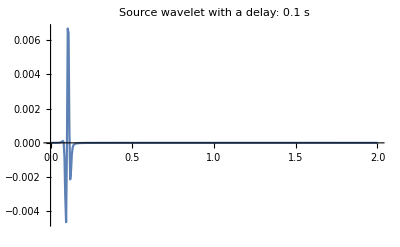

```mathematica
(*time vector*)
t=Range[Length[srcF]]/(deltafreq Length[srcF])//N;

With[{delay=.1},
ListLinePlot[{t,Re@InverseFourier@(srcF (Exp[ⅈ 2Pi# delay]&/@freqvec))}ᵀ,PlotRange->{Automatic,Full},PlotLabel->"Source wavelet with a delay: "<>ToString[delay]<>" s"]
]
```

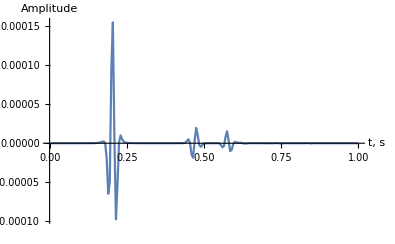

```mathematica
ListLinePlot[{t,Re@InverseFourier@(singleTrace srcF)}ᵀ,PlotRange->Full,AxesLabel->{"t, s","Amplitude"}]
```

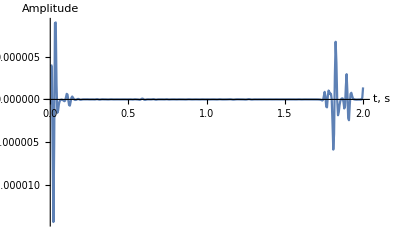

```mathematica
ListLinePlot[{t,Re@InverseFourier@(singleTrace srcF)}ᵀ,PlotRange->Full,AxesLabel->{"t, s","Amplitude"}]
```

```mathematica
gather=ParallelTable[
With[{x=x0,zs=.4,zr=.3,fmax=maxfreq},
integrateNow[#,x,{zs,zr},fmax,model,dList,ω0,{.05,1.1}]&/@freqvec//Quiet
],
{x0,0,5,.025}
]ᵀ
```

{{0.000360789+0.00224677 ⅈ,-0.00948267+0.00999569 ⅈ,0.0159052-0.00786609 ⅈ},{0.00149996+0.00149187 ⅈ,-0.00966308+0.00363236 ⅈ,0.00447607+0.0244829 ⅈ}}

```mathematica
Export[NotebookDirectory[]<>"x0-5KM_dx25M.mc",Compress[gather],"String"]
```